## Dimensionless Inorganic Carbon Partitioning

Chemical constants and CO2 evasion rate

```mathematica
conv=10^6;(*conversion factor for mmol/m^3 or μmol/l*)
T=15;(*temperature, C*)
pCO2a=420 10^-6;(*atm*)
g=9.8; 
ρ =10^3; (*kg/m3*)

(*Equilibrium constants, Stumm & Morgan 1996*)
pK1[T_]:=-(-356.309-0.0609(T+273)+21834.37/(T+273)+126.8339Log10[T+273]-1684915/(T+273)^2);
pK2[T_]:=-(-107.887-0.032528(T+273)+5151.79/(T+273)+38.92561Log10[T+273]-563713.9/(T+273)^2);
pKw[T_]:=-(-283.971+13323/(T+273)-0.0507(T+273)+102.24447Log10[T+273]-1119669/(T+273)^2);
pKHf[S_,T_]:=-Log10[Exp[9345/(T+273)-60.24+23.3585Log[(T+273)/100]+S(0.023517-0.00023656 (T+273)+0.0047036((T+273)/100)^2)]];
K1=conv 10^(-pK1[T]);K2=conv 10^(-pK2[T]);KH=conv 10^(-pKHf[0,T]);Kw=conv^2 10^(-pKw[T]);

(*CO2 evasion rate, Raymond 2013*)
Sc=1911.1-118.11 T +3.4527 T^2-0.04132 T^3;
k600[S_,U_]:= (S U 2841+2)/(3600 24);(*m/s*)
k[S_,U_,Sc_]:=k600[S,U] √(600/Sc);(*m/s*)

(*graphic options*)
opts={Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->12],TicksStyle->Directive["Label",10]};
```

### Analytical Solution

The derivation of the analytical solution of the spatially explicit model (equation 4 in the manuscript) is reported in Sec. S3 of the Supporting Information.

```mathematica
(*analytical solution*)
ATMXnorman[Πdist_,Πeq_,τratio_]:=((1-Πeq)-(1-Πdist-Πeq)ⅇ^-τratio - Πdist/τratio( 1-ⅇ^-τratio));

(*range of values for the dimensionless numbers*)
Πdistlist=Range[0,1,0.25];
Πeqlist=Join[{0.01},Range[0.25,1,0.25]];

(*Generate the shades of colors*)
Πdistcolors=ColorData["DeepSeaColors"]/@Rescale[Range[Length[Πdistlist]]];
Πeqcolors=ColorData["AvocadoColors"]/@Rescale[Range[Length[Πeqlist]]];

pΠdist=Plot[Evaluate[Table[ATMXnorman[Πdist,0.2,τratio],{Πdist,Πdistlist}]],{τratio,0,15},Evaluate[opts],
PlotRange->{All,{-0.01,1.05}},Frame->True,FrameLabel->{"τ_adv/τ_ev","ATM_X/IN_X"},
PlotLegends->Placed[LineLegend[Πdistlist,LegendLabel->"Πdist"],{1,0.6}],PlotStyle->Πdistcolors];

pΠeq=Plot[Evaluate[Table[ATMXnorman[0.2,Πeq,τratio],{Πeq,Πeqlist}]],{τratio,0,15},Evaluate[opts],
PlotRange->{All,{-0.01,1.05}},Frame->True,FrameLabel->{"τ_adv/τ_ev","ATM_X/IN_X"},
PlotLegends->Placed[LineLegend[Πeqlist,LegendLabel->"Πeq"],{1,0.6}],PlotStyle->Πeqcolors];

Grid[{{pΠdist,pΠeq}}]
```

-Graphics- | -Graphics-

### Numerical Solution

Here we solve the spatially explicit model (equation 4 in the manuscript) for specific values of the dimensionless parameters. The goal is to compare the results with the analytical solution.

```mathematica
(*river hydrodynamics*)
Lriv=50000; (*m*)
Q = 10; (*m^3/s*)

(*scaling laws; not that the use of the scaling laws is not necessary, it is just a way to reduce simulation inputs *)
U=ⅇ^-1.06 Q^0.1;(*Raymond USGS station data*)
b=ⅇ^1.86 Q^0.5;
h =ⅇ^-0.8 Q^0.4;
S=0.021 (0.0283)^0.5 Q^-0.5;(*Leopold 1953, pag 619*)
Fr = U/√(g h);(*Froude*)

(*timescales*)
τadv= Lriv/U;
τev= h/k[S,U,Sc];

(*initial conditions water chemistry*)
CO2wa=KH pCO2a; (*equilibrium CO2w*)
CO2w0=100CO2wa;
pH0=6;
H0 = conv 10^-pH0;
OH0 = Kw/H0;
HCO30 =K1 CO2w0/H0;
CO30=K1 K2 CO2w0/H0^2;
DIC0=CO2w0+HCO30+CO30;
Alk0=HCO30+2 CO30+Kw/H0-H0;

(*inputs*)
IC0 = DIC0 Q; (*initial, μmol/s*)
Πdist=0.2;
ICX= IC0/(1-Πdist);(*total*)
IClatdiff= Πdist ICX;(*lateral*)

(*carbonate system*)
CarbEq[x_]:={HCO3[x]==K1 CO2w[x]/H[x], CO3[x]==K1 K2 CO2w[x]/H[x]^2,DIC[x]==CO2w[x]+HCO3[x]+CO3[x],Alk0==HCO3[x]+2 CO3[x]+Kw/H[x]-H[x]};

(*DIC mass balance*)
ATM[x_]:=k[S,U,Sc] b(CO2wa-CO2w[x]);(*μmol/m s*)
BIO[x_]:=0;(*- b h NEP;*)(*μmol/m s*)
LAT[x_]:=IClatdiff/Lriv;
eqDIC[x_]:={D[Q DIC[x],x]== ATM[x]+LAT[x]+BIO[x]};

sol=NDSolve[(Flatten[{eqDIC[x],CarbEq[x],DIC[0]==DIC0,CO2w[0]==CO2w0,HCO3[0]==HCO30,CO3[0]==CO30,H[0]==conv 10^-pH0}]),{DIC,CO2w,HCO3,CO3,H},{x,0,Lriv}];
```

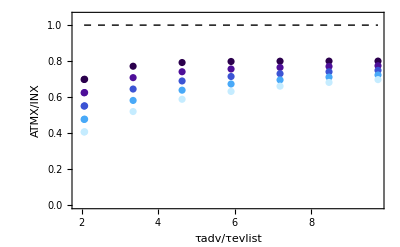

```mathematica
(*multiple simulations with different distributed inputs*)

(*varying τev*)
Slist=Join[{10^-10},{10^-5},Range[10^-3,6 10^-3,10^-3]];
klist=Table[k[Sp,U,Sc],{Sp,Slist}];(*m/s*)
τevlist= h/klist;(*evasion length*)

(*IC eq*)
Alk0 = 100;
solHeq =  NSolve[{H>0,Alk0==K1 CO2wa/H+2 K1 K2 CO2wa/H^2+Kw/H-H},H][[1]][[1]][[2]];
DICeq=(K1 CO2wa/H+K1 K2 CO2wa/H^2+CO2wa)/.H->solHeq;
ICeq= DICeq U;
Πeq=0.2;

(*varying α and input partitioning*)
αlist = Range[0,1,0.25];
ICX = ICeq /Πeq;
IC0list= (1-Πdistlist)ICX;(*total*)
IClatlist= Πdistlist ICX;(*total*)

(*chemical solver*)
C2[Alk0_,DIC0_]:=NSolve[Flatten[{(CarbEq[0]/.{Alk[0]->Alk0,DIC[0]->DIC0}),H[0]>0}],{CO2w[0],HCO3[0],CO3[0],H[0]}];

(*initialization*)
DIC0list= Table[0,{rows,Length[Πdistlist]},{columns,1}];
ICoutlist=Table[0,{rows,Length[Πdistlist]},{columns,Length[Slist]}];
ATMxlist=Table[0,{rows,Length[Πdistlist]},{columns,Length[Slist]}];

(*cycle*)
Off[NIntegrate::ncvb]
For[i=1,i<=Length[Πdistlist],i++,
For[j=1,j<=Length[τevlist],j++,
(*evasion*)
ATM[x_]:=klist[[j]]/h(CO2wa-CO2w[x]);(*μmol/m s*)
(*inputs*)
LAT[x_]:= IClatlist[[i]]/Lriv;(*lateral*)
(*DIC0 to satisfy the Πdist*)
DIC0list[[i]]=IC0list[[i]]/U;
(*initial chemistry condition*)
{CO2w0,HCO30,CO30,H0}={CO2w[0],HCO3[0],CO3[0],H[0]}/.C2[Alk0,DIC0list[[i]]][[1]];
(*solver*)
eqDIC[x_]:={U D[DIC[x],x]== ATM[x]+LAT[x]+BIO[x]};sol=NDSolve[(Flatten[{eqDIC[x],CarbEq[x],DIC[0]==DIC0list[[i]],CO2w[0]==CO2w0,HCO3[0]==HCO30,CO3[0]==CO30,H[0]==H0}]),{DIC,CO2w,HCO3,CO3,H},{x,0,Lriv}];
(*results*)
ICoutlist[[i,j]]=Q((DIC[Lriv])/.sol)[[1]];
ATMxlist[[i,j]]=NIntegrate[(-ATM[x]/.sol)[[1]],{x,0,Lriv}];
]]
(*Budyko's plots*)
pΠdistnum=ListPlot[Transpose[{τadv/τevlist,#}]&/@(ATMxlist/ICX),PlotStyle->Πdistcolors,PlotRange->{All,{0,1.05}},Frame->True,FrameLabel->{"τadv/τevlist","ATMX/INX"},Mesh->All,Epilog->{Dashed,Black,Line[{{Min[τadv/τevlist],1},{Max[τadv/τevlist],1}}]}
]
```

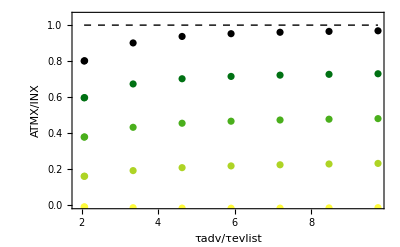

```mathematica
(*multiple simulations with different Πeq (i.e., alkalinity)*)
ICX1=1000;
DIC0 = ICX1(1-Πdist)/U;
Πeqlist= Join[{0.01},Range[0.25,1,0.25]];
ICeqlist= ICX1 Πeqlist;
DICeqlist=ICeqlist/ U;

(*initialization*)
Alk0list=Table[0,{rows,Length[Πeqlist]},{columns,1}];
ICoutlist1=Table[0,{rows,Length[Πeqlist]},{columns,Length[Slist]}];
ATMxlist1=Table[0,{rows,Length[Πeqlist]},{columns,Length[Slist]}];

(*cycle*)
Off[NIntegrate::ncvb]
For[i=1,i<=Length[Πeqlist],i++,
For[j=1,j<=Length[τevlist],j++,

(*initial chemistry condition*)
solHeq =  NSolve[{H>0,DICeqlist[[i]]==CO2wa+K1 CO2wa/H+2 K1 K2 CO2wa/H^2},H][[1]][[1]][[2]];
Alk0list[[i]] = (K1 CO2wa/H+2 K1 K2 CO2wa/H^2+Kw/H-H)/.H->solHeq;

CarbEq[x_]:={HCO3[x]==K1 CO2w[x]/H[x], CO3[x]==K1 K2 CO2w[x]/H[x]^2,DIC[x]==CO2w[x]+HCO3[x]+CO3[x],Alk0list[[i]]==HCO3[x]+2 CO3[x]+Kw/H[x]-H[x]};
{CO2w0,HCO30,CO30,H0}={CO2w[0],HCO3[0],CO3[0],H[0]}/.C2[Alk0list[[i]],DIC0][[1]];

(*evasion*)
ATM[x_]:=klist[[j]]/h(CO2wa-CO2w[x]);(*μmol/m s*)
(*lateral inputs*)
LAT[x_]:= ICX1 Πdist/Lriv;(*lateral*)

(*main eq*)
eqDIC[x_]:={U D[DIC[x],x]== ATM[x]+LAT[x]+BIO[x]};

(*solution*)sol=NDSolve[(Flatten[{eqDIC[x],CarbEq[x],DIC[0]==DIC0,CO2w[0]==CO2w0,HCO3[0]==HCO30,CO3[0]==CO30,H[0]==H0}]),{DIC,CO2w,HCO3,CO3,H},{x,0,Lriv}];

(*results*)
ICoutlist1[[i,j]]=Q((DIC[Lriv])/.sol)[[1]];
ATMxlist1[[i,j]]=NIntegrate[(-ATM[x]/.sol)[[1]],{x,0,Lriv}];
]]
(*Budyko's plots*)
pΠeqnum=ListPlot[Transpose[{τadv/τevlist,#}]&/@(ATMxlist1/ICX1),PlotStyle->Πeqcolors,PlotRange->{All,{0,1.05}},Frame->True,FrameLabel->{"τadv/τevlist","ATMX/INX"},Mesh->All,Epilog->{Dashed,Black,Line[{{Min[τadv/τevlist],1},{Max[τadv/τevlist],1}}]}
]
```

### Final figure, analytical and numerical solutions

```mathematica
(*combining analytical and numerical results from previous sections*)
GraphicsGrid[{{Show[{pΠdist,pΠdistnum,PlotRange->{{0,15},{0,1}}}],Show[{pΠeq,pΠeqnum,PlotRange->{{0,15},{0,1}}}]}}]
```

-Graphics-